# Fractal Substitution by L-system (the Spectre Tile)

## Begin With Edges

```mathematica
edgeProduce={e[_][dir_]:>ReIm[Exp[dir*Pi/6 I]]};
```

```mathematica
edgeReplaceRule=
{
(*even to odd replace rule*)
{e[11][dir_],e[10][_],e[9][_],e[8][_],e[7][_],e[6][_]}:>{
e[4][dir+4],e[5][dir+1],
e[6][dir-1],e[7][dir+2],e[8][dir],e[9][dir+3],e[10][dir+1],e[11][dir+4],
e[12][dir+2],e[13][dir+2],e[14][dir+4],e[1][dir+1]},

{e[5][dir_],e[4][_]}:>{
e[2][dir-4],e[3][dir-1],
e[12][dir-3],e[13][dir-3],e[14][dir-1],e[1][dir-4],
e[2][dir-2],e[3][dir+1]},

{e[3][dir_],e[2][_]}:>{
e[4][dir+4],e[5][dir+1],
e[2][dir-1],e[3][dir+2],
e[12][dir],e[13][dir],e[14][dir+2],e[1][dir-1]},

{e[1][dir_],e[14][_],e[13][_],e[12][_]}:>{
e[2][dir-4],e[3][dir-1],
e[12][dir-3],e[13][dir-3],e[14][dir-1],e[1][dir-4],
e[2][dir-2],e[3][dir+1],
e[4][dir+3],e[5][dir],
e[2][dir-2],e[3][dir+1],
e[12][dir-1],e[13][dir-1],e[14][dir+1],e[1][dir-2],
e[2][dir],e[3][dir+3]
}
,
(*odd to even replace rule*)
{e[6][_],e[7][_],e[8][_],e[9][_],e[10][_],e[11][dir_]}:>{
e[1][-1+dir],e[14][-4+dir],e[13][-2+dir],e[12][-2+dir],
e[11][-4+dir],e[10][-1+dir],e[9][-3+dir],e[8][dir],e[7][-2+dir],e[6][1+dir],
e[5][-1+dir],e[4][-4+dir]},

{e[4][_],e[5][dir_]}:>{
e[3][-1+dir],e[2][2+dir],
e[1][4+dir],e[14][1+dir],e[13][3+dir],e[12][3+dir],
e[3][1+dir],e[2][4+dir]},

{e[2][_],e[3][dir_]}:>{
e[1][1+dir],e[14][-2+dir],e[13][dir],e[12][dir],
e[3][-2+dir],e[2][1+dir],
e[5][-1+dir],e[4][-4+dir]},

{e[12][_],e[13][_],e[14][_],e[1][dir_]}:>{
e[3][-3+dir],e[2][dir],
e[1][2+dir],e[14][-1+dir],e[13][1+dir],e[12][1+dir],
e[3][-1+dir],e[2][2+dir],
e[5][dir],e[4][-3+dir],
e[3][-1+dir],e[2][2+dir],
e[1][4+dir],e[14][1+dir],e[13][3+dir],e[12][3+dir],
e[3][1+dir],e[2][4+dir]}
};
```

```mathematica
basicEdges[dir_]:={
e[11][2+dir],e[10][5+dir],e[9][3+dir],e[8][6+dir],e[7][4+dir],e[6][7+dir],
e[5][9+dir],e[4][6+dir],
e[3][8+dir],e[2][11+dir],
e[1][1+dir],e[14][-2+dir],e[13][dir],e[12][dir]};
```

```mathematica
substitute["e"][edgeList_List]:=Catenate[SequenceReplace[edgeList,edgeReplaceRule]]
```

```mathematica
buildTileBoundary[or_:{0,0},dir_:0,level_:0]:=FoldList[
Plus,or,Nest[substitute["e"],basicEdges[dir],level]/.edgeProduce
]
```

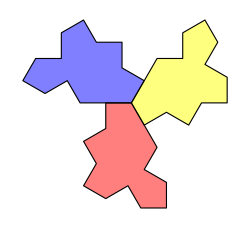
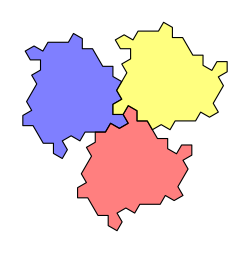
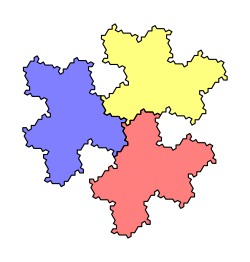
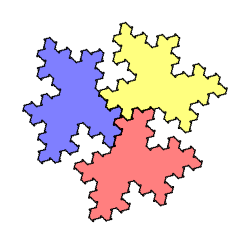

```mathematica
Graphics[{
EdgeForm[Black],Opacity[.5],
Blue,Polygon[buildTileBoundary[{0,0},0,#]],
Red,Polygon[buildTileBoundary[{0,0},4,#]],
Yellow,Polygon[buildTileBoundary[{0,0},8,#]]
},ImageSize->250]&/@Range[0,3]//Row
```

## Treat Edges Segment as a Whole

```mathematica
EToEdges={
(*even*)
E[1][dir_]:>{e[11][dir],e[10][3+dir],e[9][1+dir],e[8][4+dir],e[7][2+dir],e[6][5+dir]},
E[2][dir_]:>{e[5][dir],e[4][dir-3]},
E[3][dir_]:>{e[3][dir],e[2][dir+3]},
E[4][dir_]:>{e[1][dir],e[14][dir-3],e[13][dir-1],e[12][dir-1]},
(*odd*)
E[5][dir_]:>{e[6][-5+dir],e[7][-2+dir],e[8][-4+dir],e[9][-1+dir],e[10][-3+dir],e[11][dir]},
E[6][dir_]:>{e[4][3+dir],e[5][dir]},
E[7][dir_]:>{e[2][-3+dir],e[3][dir]},
E[8][dir_]:>{e[12][1+dir],e[13][1+dir],e[14][3+dir],e[1][dir]}
};
```

```mathematica
basicE[dir_,False]:={E[1][2+dir],E[2][9+dir],E[3][8+dir],E[4][1+dir]};
```

```mathematica
basicE[dir_,True]:={E[8][-1+dir],E[7][-8+dir],E[6][-9+dir],E[5][-2+dir]};
```

```mathematica
EReplaceRule={
E[1][dir_]:>{E[6][1+dir],E[5][4+dir],E[8][1+dir]},
E[2][dir_]:>{E[7][dir-1],E[8][dir-4],E[7][1+dir]},
E[3][dir_]:>{E[6][1+dir],E[7][2+dir],E[8][dir-1]},
E[4][dir_]:>{E[7][dir-1],E[8][dir-4],E[7][dir+1],E[6][dir],E[7][dir+1],E[8][dir-2],E[7][dir+3]},

E[5][dir_]:>{E[4][-1+dir],E[1][-4+dir],E[2][-1+dir]},
E[6][dir_]:>{E[3][-1+dir],E[4][4+dir],E[3][1+dir]},
E[7][dir_]:>{E[4][1+dir],E[3][-2+dir],E[2][-1+dir]},E[8][dir_]:>{E[3][-3+dir],E[4][2+dir],E[3][-1+dir],E[2][dir],E[3][-1+dir],E[4][4+dir],E[3][1+dir]}
};
```

```mathematica
substitute["E"][edgeList_List]:=Catenate[ReplaceAll[edgeList,EReplaceRule]]
```

### Depict Single Tile

```mathematica
buildTileBoundary[or_:{0,0},dir_:0,level_:0,OptionsPattern[{"Parity"->False}]]:=FoldList[
Plus,or,Catenate[Nest[substitute["E"],RotateLeft[#,1]&@basicE[dir,OptionValue["Parity"]],level]/.EToEdges]/.edgeProduce
]
```

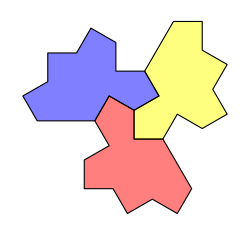
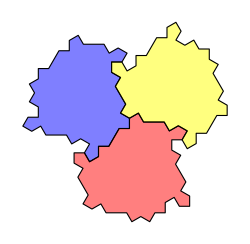
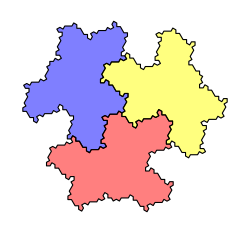
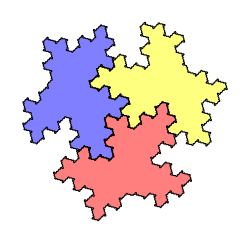

```mathematica
Graphics[{
EdgeForm[Black],Opacity[.5],
Function[{r,p},
{Blue,Polygon[buildTileBoundary[{0,0},r,#,"Parity"->p]],
Red,Polygon[buildTileBoundary[{0,0},r+4,#,"Parity"->p]],
Yellow,Polygon[buildTileBoundary[{0,0},r+8,#,"Parity"->p]]
}][0,True]
},ImageSize->250]&/@Range[0,3]//Row
```

### Depict Tile Details/Tiling

```mathematica
completeTile=Append[
Switch[
First[Head[#]],
1,RotateLeft[basicE[First[#]-2,False],0],
2,RotateLeft[basicE[First[#]-9,False],1],
3,RotateLeft[basicE[First[#]-8,False],2],
4,RotateLeft[basicE[First[#]-1,False],3],
5,RotateLeft[basicE[First[#]+2,True],-1],
6,RotateLeft[basicE[First[#]+9,True],-2],
7,RotateLeft[basicE[First[#]+8,True],-3],
8,RotateLeft[basicE[First[#]+1,True],0]
]
,#
]&;
```

#### Use Line to draw

```mathematica
depictTilingLine[or_:{0,0},dir_:0,level_:0,OptionsPattern[{"Parity"->False}]]:=FoldList[
Plus,or,Catenate[Nest[Catenate[completeTile/@substitute["E"][#]]&,basicE[dir,OptionValue["Parity"]],level]/.EToEdges]/.edgeProduce
]
```

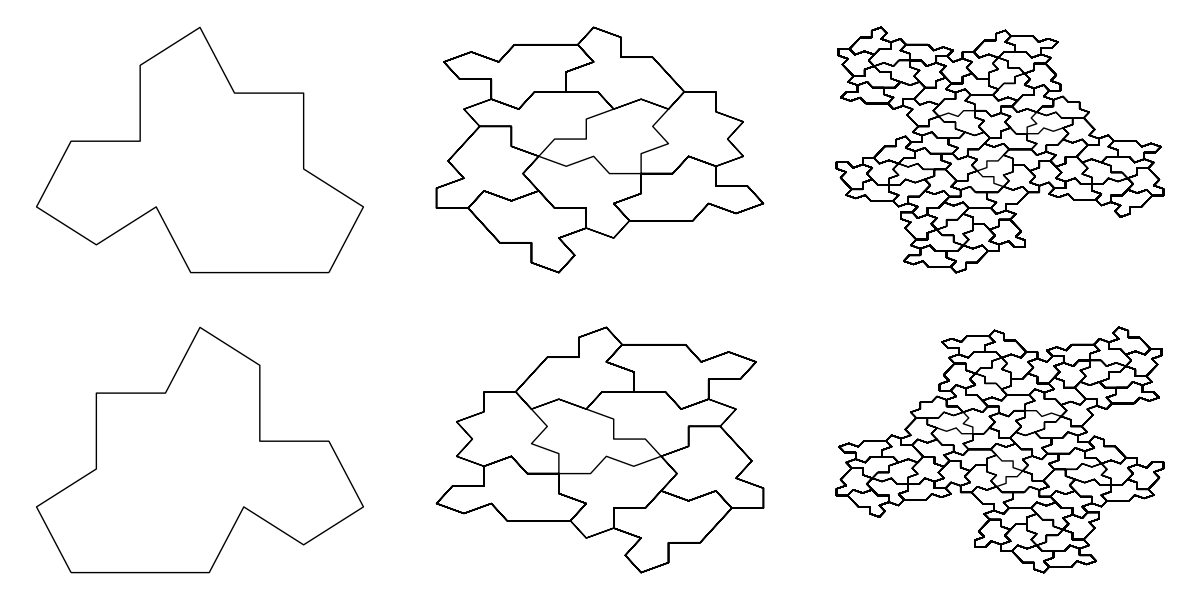

```mathematica
Outer[
Graphics[Line[depictTilingLine[{0,0},0,#2,"Parity"->#1]]]&
,{False,True},Range[0,2]
]//Grid
```

#### Obtain Polygons

```mathematica
buildTilingPolygons[o_:{0,0},dir_:0,level_:0,OptionsPattern[{"Parity"->False}]]:=First@Last@Reap[
Module[{or=o},
Scan[
(Sow[Polygon[FoldList[Plus,or,Catenate[#[[;;-2]]/.EToEdges/.edgeProduce]]]];
or=Fold[Plus,or,#[[1]]/.EToEdges/.edgeProduce])&,
Nest[
Map[completeTile,#/.EReplaceRule,{-2}]&,
If[level===0,Append[#,First[#]]&,Identity]@
basicE[dir,OptionValue["Parity"]],
level]
,{-3}
]
]
];
```

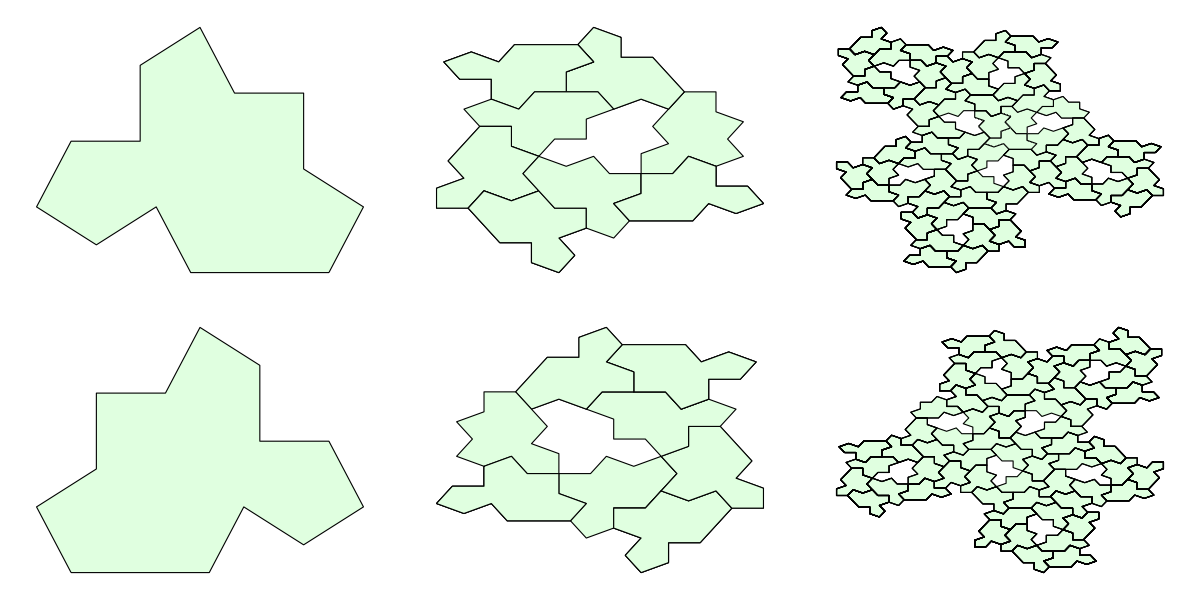

```mathematica
Outer[
Graphics[{LightGreen,EdgeForm[Black],buildTilingPolygons[{0,0},0,#2,"Parity"->#1]}]&
,{False,True},Range[0,2]
]//Grid
```